```mathematica
The code for  the post filtering of the 911 parameter sets which were estimated by the simulated annealing
```

```mathematica
Detailed description of the parameter estimation procedure  using post filetering  can be found in Materials and Methods and Fig EV2B-F.
```

```mathematica
(*Experimental data (human PRCs to a 3 h light pulse, 6.7 h light pulse and 3 cycle 5 h light pulses) were adopted from the following references

References
1.The human PRC to 3h light prc:
Minors DS,Waterhouse JM,Wirz-Justice A (1991) A human phase-response curve to light.Neuroscience letters 133:36-40;
2.The human PRC to 6.7h light prc:
Khalsa SB,Jewett ME,Cajochen C,Czeisler CA (2003) A phase response curve to single bright light pulses in human subjects.The Journal of physiology 549:945-952;
3.The human PRC to 3-cycle 5 h light prc:
Khalsa SBS,Jewett ME,Klerman EB,Duffy JE,Rimmer DW,Kronauer RE,Czeisler CA (1997) Type 0 resetting of the human circadian pacemaker to consecutive bright light pulses against a background of very dim light. .Sleep Res 26:722;
*)

simulcolor=RGBColor[252/255,164/255,4/255];
expcolor=Black;
meancolor=RGBColor[156/255,156/255,156/255];


expprc3hlightpulse=Import["C:\\Users\\user\\Desktop\\code\\data\\exp_prc3hlightpulse.xls"][[1]];
expprc67hlightpulse=Import["C:\\Users\\user\\Desktop\\code\\data\\exp_prc67hlightpulse.xls"][[1]];
expprc3cyclelightpulse=Import["C:\\Users\\user\\Desktop\\code\\data\\exp_prc3cyclelightpulse.xls"][[1]];
ex3hrgraph=ListPlot[expprc3hlightpulse,PlotRange->{{0,24},{-4,4}},PlotStyle->expcolor];
ex67hrgraph=ListPlot[expprc67hlightpulse,PlotRange->{{0,24},{-4.5,4.5}},PlotStyle->expcolor];
ex3cyclegraph=ListPlot[expprc3cyclelightpulse,PlotRange->{{0,24},{-12,12}},PlotStyle->expcolor];
```

```mathematica
(*The 911 parameter sets which estimated by the simulated annealing methods*)
class=Import["C:\\Users\\user\\Desktop\\code\\data\\totalparaset.xls"][[1]];

(*The PRCs to 3 h light pulse, 6.7 h light pulse, 12 h light pulse and 3-cycle 5 h light pulse which were simulated by the model with the 911 pairs of gating and adpatation*)
prc3hrclass=Import["C:\\Users\\user\\Desktop\\code\\data\\totalprc3hr.xls"][[1]];
prc67hrclass=Import["C:\\Users\\user\\Desktop\\code\\data\\totalprc67hr.xls"][[1]];
prc12hrclass=Import["C:\\Users\\user\\Desktop\\code\\data\\totalprc12hr.xls"][[1]];
prc3cycleclass=Import["C:\\Users\\user\\Desktop\\code\\data\\totalprc3cycle.xls"][[1]];

(*The phase delays induced by 3-day LD dosing at ZT11 which were simulated by the model with the 911 pairs of gating and adpatation*)
ldzt10class=Import["C:\\Users\\user\\Desktop\\code\\data\\totallddosingzt10.xls"][[1]];
```

```mathematica
(*graphical illustration of the 911 pairs of gating and adaptation which were filtered out*)
set={};
For[i=1,i<Dimensions[class][[1]]+1,i++,
set=Join[set,{{class[[i]][[5]],class[[i]][[6]],class[[i]][[3]],class[[i]][[4]],class[[i]][[2]],class[[i]][[1]]-24+class[[i]][[2]]}}];
];

adapcollect={};
gatingcollect={};

opa=0.12;
ft=18;

For[i=1,i<Dimensions[set][[1]]+1,i++,

scale=set[[i]][[1]];
exponent=set[[i]][[2]];
perconst1=set[[i]][[3]];
perconst2=set[[i]][[4]];
interval=set[[i]][[5]];
rotate=set[[i]][[6]]*10;

adap[x_]:=-(x^exponent/(x^exponent+scale^exponent))+1;

pergating=NonlinearModelFit[{{24-interval,perconst1},{24,perconst1},{24-0.5*interval,perconst2}},q0+q1*x+q2*x^2+q3*x^3+q4*x^4,{q0,q1,q2,q3,q4},x];

interpol=Join[Table[perconst1,{x,0,24-interval,0.1}],Table[pergating[x],{x,24-interval+0.1,24,0.1}]];
interpol=RotateRight[interpol,rotate];
gatingcollect=Join[gatingcollect,{Table[interpol[[i+1]],{i,0,240}]}];
adapcollect=Join[adapcollect,{Table[adap[0.1*i],{i,0,240}]}];
];

classgraph=ListPlot[gatingcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[Black]];
adapgraph=ListPlot[adapcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.5,1},{"100","","0"}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[Black]];

meangating=Mean[gatingcollect];
meanadap=Mean[adapcollect];

meangatinggraph=ListPlot[meangating,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","6","","12"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[meancolor]];
meanadapgraph=ListPlot[meanadap,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{0,6,12,18,24}}],Transpose[{{0,0.5,1},{0,50,100}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[meancolor]];

ft=18;

nhp10ld={-0.850731324125,-1.78384314975,-1.6757049756250002};
nhp10ldsem={0.1007230677173346,0.30427558193544485,0.27312765171698605};

For[i=1,i<Dimensions[class][[1]]+1,i++,
ldzt10class[[i]]=Join[{0},ldzt10class[[i]]];
];

ld10graph=ListPlot[ldzt10class,DataRange->{0,3},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,-3},Ticks->{Transpose[{{0,1,2,3},{"0","1","2","3"}}],Transpose[{{-3,-2,-1,0},{"-3","-2","-1","0"}}]},PlotRange->{{0,3.1},{-3,0}},TicksStyle->Directive[Black]];
meanld10graph=ListPlot[Mean[ldzt10class],DataRange->{0,3},Joined->True,PlotStyle->Directive[meancolor],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,-3},Ticks->{Transpose[{{0,1,2,3},{"0","1","2","3"}}],Transpose[{{-3,-2,-1,0},{"-3","-2","-1","0"}}]},PlotRange->{{0,3.1},{-3,0}},TicksStyle->Directive[Black]];

Needs["ErrorBarPlots`"]
expnhp10ldgraph=ErrorListPlot[{{{1,nhp10ld[[1]]},ErrorBar[nhp10ldsem[[1]]]},{{2,nhp10ld[[2]]},ErrorBar[nhp10ldsem[[2]]]},{{3,nhp10ld[[3]]},ErrorBar[nhp10ldsem[[3]]]}},PlotStyle->Black];

GraphicsGrid[{{Show[ld10graph,meanld10graph,expnhp10ldgraph],Show[classgraph,meangatinggraph],Show[adapgraph,meanadapgraph]}}]
```

-Graphics-

```mathematica
(*Measurment of the amplitdue of the simulated PRCs*)
camp3={};
camp67={};
camp12={};
For[i=1,i<Dimensions[prc3hrclass][[1]]+1,i++,
camp3=Join[camp3,{Max[prc3hrclass[[i]]]-Min[prc3hrclass[[i]]]}];
camp67=Join[camp67,{Max[prc67hrclass[[i]]]-Min[prc67hrclass[[i]]]}];
camp12=Join[camp12,{Max[prc12hrclass[[i]]]-Min[prc12hrclass[[i]]]}];
];
```

```mathematica
(*152 pairs of gating and aadaptation with which simulated PRCs to a 12 h light pulse are discontinuous were filtesimulcolor out*)
fclass1={};
fprc3hrclass1={};
fprc67hrclass1={};
fprc12hrclass1={};
fldzt10class1={};
fprc3cycleclass1={};

fclass2={};
fprc3hrclass2={};
fprc67hrclass2={};
fprc12hrclass2={};
fldzt10class2={};
fprc3cycleclass2={};

exclass2={};
exprc3hrclass2={};
exprc67hrclass2={};
exprc12hrclass2={};
exldzt10class2={};
exprc3cycleclass2={};

For[i=1,i<Dimensions[class][[1]]+1,i++,

If[camp12[[i]]<8,

fclass1=Join[fclass1,{class[[i]]}];
fprc3hrclass1=Join[fprc3hrclass1,{prc3hrclass[[i]]}];
fprc67hrclass1=Join[fprc67hrclass1,{prc67hrclass[[i]]}];
fprc12hrclass1=Join[fprc12hrclass1,{prc12hrclass[[i]]}];
fldzt10class1=Join[fldzt10class1,{ldzt10class[[i]]}];
fprc3cycleclass1=Join[fprc3cycleclass1,{prc3cycleclass[[i]]}];
,

exclass2=Join[exclass2,{class[[i]]}];
exprc3hrclass2=Join[exprc3hrclass2,{prc3hrclass[[i]]}];
exprc67hrclass2=Join[exprc67hrclass2,{prc67hrclass[[i]]}];
exprc12hrclass2=Join[exprc12hrclass2,{prc12hrclass[[i]]}];
exldzt10class2=Join[exldzt10class2,{ldzt10class[[i]]}];
exprc3cycleclass2=Join[exprc3cycleclass2,{prc3cycleclass[[i]]}];

];

];

(*Double checking whether the model with the excluded parameter sets has the type 0 prc using the hourly sample data set of 12 h light prc*)
prc12hr2ndfinefiltering=Import["C:\\Users\\user\\Desktop\\code\\data\\prc12hr2ndfinefiltering.xls"][[1]];

For[i=1,i<Dimensions[prc12hr2ndfinefiltering][[1]]+1,i++,

If[(Max[prc12hr2ndfinefiltering[[i]]]-Min[prc12hr2ndfinefiltering[[i]]])<11,

fclass1=Join[fclass1,{exclass2[[i]]}];
fprc3hrclass1=Join[fprc3hrclass1,{exprc3hrclass2[[i]]}];
fprc67hrclass1=Join[fprc67hrclass1,{exprc67hrclass2[[i]]}];
fprc12hrclass1=Join[fprc12hrclass1,{exprc12hrclass2[[i]]}];
fldzt10class1=Join[fldzt10class1,{exldzt10class2[[i]]}];
fprc3cycleclass1=Join[fprc3cycleclass1,{exprc3cycleclass2[[i]]}];
,

fclass2=Join[fclass2,{exclass2[[i]]}];
fprc3hrclass2=Join[fprc3hrclass2,{exprc3hrclass2[[i]]}];
fprc67hrclass2=Join[fprc67hrclass2,{exprc67hrclass2[[i]]}];
fprc12hrclass2=Join[fprc12hrclass2,{exprc12hrclass2[[i]]}];
fldzt10class2=Join[fldzt10class2,{exldzt10class2[[i]]}];
fprc3cycleclass2=Join[fprc3cycleclass2,{exprc3cycleclass2[[i]]}];
];

];

(*{the number of parameter sets, which were filtered in, the number of parameter sets, which were filetered our}*)
Print[{Dimensions[fclass1][[1]],Dimensions[fclass2][[1]]}];
```

{759,152}

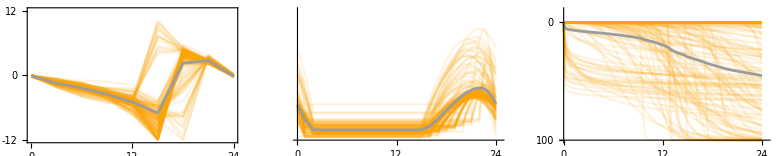

```mathematica
(*graphical illustration of the 152 pairs of gating and adaptation which were filtered out*)
set={};
For[i=1,i<Dimensions[fclass2][[1]]+1,i++,
set=Join[set,{{fclass2[[i]][[5]],fclass2[[i]][[6]],fclass2[[i]][[3]],fclass2[[i]][[4]],fclass2[[i]][[2]],fclass2[[i]][[1]]-24+fclass2[[i]][[2]]}}];
];

adapcollect={};
gatingcollect={};

opa=0.12;
ft=18;

For[i=1,i<Dimensions[set][[1]]+1,i++,

scale=set[[i]][[1]];
exponent=set[[i]][[2]];
perconst1=set[[i]][[3]];
perconst2=set[[i]][[4]];
interval=set[[i]][[5]];
rotate=set[[i]][[6]]*10;

adap[x_]:=-(x^exponent/(x^exponent+scale^exponent))+1;

pergating=NonlinearModelFit[{{24-interval,perconst1},{24,perconst1},{24-0.5*interval,perconst2}},q0+q1*x+q2*x^2+q3*x^3+q4*x^4,{q0,q1,q2,q3,q4},x];

interpol=Join[Table[perconst1,{x,0,24-interval,0.1}],Table[pergating[x],{x,24-interval+0.1,24,0.1}]];
interpol=RotateRight[interpol,rotate];
gatingcollect=Join[gatingcollect,{Table[interpol[[i+1]],{i,0,240}]}];
adapcollect=Join[adapcollect,{Table[adap[0.1*i],{i,0,240}]}];
];

classgraph=ListPlot[gatingcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[Black]];

adapgraph=ListPlot[adapcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.5,1},{"100","","0"}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[Black]];

meangating=Mean[gatingcollect];
meanadap=Mean[adapcollect];

meangatinggraph=ListPlot[meangating,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","6","","12"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[meancolor]];
meanadapgraph=ListPlot[meanadap,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{0,6,12,18,24}}],Transpose[{{0,0.5,1},{0,50,100}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[meancolor]];

ft=18;

meancp12=Mean[fprc12hrclass2];

cp12graph=ListPlot[fprc12hrclass2,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-12.1,12.1},Joined->True,FrameTicks->{{0,12,24},{-12,0,12}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Dashed];

meancp12graph=ListPlot[meancp12,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-12.1,12.1},Joined->True,FrameTicks->{{0,12,24},{-12,-6,0,6,12}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->{meancolor,Thickness[0.005]}];

GraphicsGrid[{{Show[cp12graph,meancp12graph],Show[classgraph,meangatinggraph],Show[adapgraph,meanadapgraph]}}]
```

```mathematica
(*323 pairs of gating and adaptation were filtered out with which simulated light PRCs to a 6.7 h light pulse have a too large phase shift between CT0 and CT6 due to overestimated photosensitivity*)

ffclass1={};
ffprc3hrclass1={};
ffprc67hrclass1={};
ffprc12hrclass1={};
ffldzt10class1={};
ffprc3cycleclass1={};

ffclass2={};
ffprc3hrclass2={};
ffprc67hrclass2={};
ffprc12hrclass2={};
ffldzt10class2={};
ffprc3cycleclass2={};

For[i=1,i<Dimensions[fclass1][[1]]+1,i++,

If[fprc67hrclass1[[i]][[2]]>fprc67hrclass1[[i]][[3]]&&fprc67hrclass1[[i]][[3]]>fprc67hrclass1[[i]][[4]],

ffclass1=Join[ffclass1,{fclass1[[i]]}];
ffprc3hrclass1=Join[ffprc3hrclass1,{fprc3hrclass1[[i]]}];
ffprc67hrclass1=Join[ffprc67hrclass1,{fprc67hrclass1[[i]]}];
ffprc12hrclass1=Join[ffprc12hrclass1,{fprc12hrclass1[[i]]}];
ffldzt10class1=Join[ffldzt10class1,{fldzt10class1[[i]]}];
ffprc3cycleclass1=Join[ffprc3cycleclass1,{fprc3cycleclass1[[i]]}];
,

ffclass2=Join[ffclass2,{fclass1[[i]]}];
ffprc3hrclass2=Join[ffprc3hrclass2,{fprc3hrclass1[[i]]}];
ffprc67hrclass2=Join[ffprc67hrclass2,{fprc67hrclass1[[i]]}];
ffprc12hrclass2=Join[ffprc12hrclass2,{fprc12hrclass1[[i]]}];
ffldzt10class2=Join[ffldzt10class2,{fldzt10class1[[i]]}];
ffprc3cycleclass2=Join[ffprc3cycleclass2,{fprc3cycleclass1[[i]]}];

 ];
];

(*{the number of parameter sets, which were filtered in, the number of parameter sets, which were filetered our}*)
Print[{Dimensions[ffclass1],Dimensions[ffclass2]}]
```

{{436,6},{323,6}}

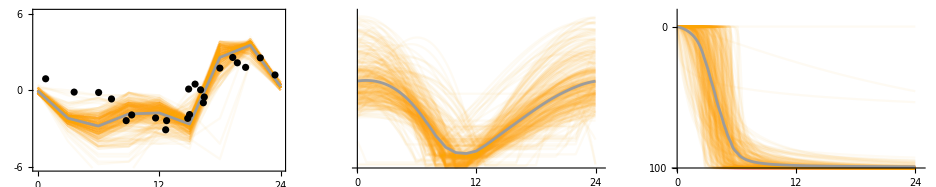

```mathematica
(*graphical illustration of the 323 pairs of gating and adaptation which were filtered out*)
adapcollect={};
gatingcollect={};

opa=0.05;
ft=18;

set={};
For[i=1,i<Dimensions[ffclass2][[1]]+1,i++,
set=Join[set,{{ffclass2[[i]][[5]],ffclass2[[i]][[6]],ffclass2[[i]][[3]],ffclass2[[i]][[4]],ffclass2[[i]][[2]],ffclass2[[i]][[1]]-24+ffclass2[[i]][[2]]}}];
];

For[i=1,i<Dimensions[set][[1]]+1,i++,

scale=set[[i]][[1]];
exponent=set[[i]][[2]];
perconst1=set[[i]][[3]];
perconst2=set[[i]][[4]];
interval=set[[i]][[5]];
rotate=set[[i]][[6]]*10;

adap[x_]:=-(x^exponent/(x^exponent+scale^exponent))+1;

pergating=NonlinearModelFit[{{24-interval,perconst1},{24,perconst1},{24-0.5*interval,perconst2}},q0+q1*x+q2*x^2+q3*x^3+q4*x^4,{q0,q1,q2,q3,q4},x];

interpol=Join[Table[perconst1,{x,0,24-interval,0.1}],Table[pergating[x],{x,24-interval+0.1,24,0.1}]];
interpol=RotateRight[interpol,rotate];
gatingcollect=Join[gatingcollect,{Table[interpol[[i+1]],{i,0,240}]}];
adapcollect=Join[adapcollect,{Table[adap[0.1*i],{i,0,240}]}];
];

classgraph=ListPlot[gatingcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[Black]];

adapgraph=ListPlot[adapcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.5,1},{"100","","0"}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[Black]];

meangating=Mean[gatingcollect];
meanadap=Mean[adapcollect];

meangatinggraph=ListPlot[meangating,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","6","","12"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[meancolor]];
meanadapgraph=ListPlot[meanadap,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{0,6,12,18,24}}],Transpose[{{0,0.5,1},{0,50,100}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[meancolor]];

ft=18;

meancp6=Mean[ffprc67hrclass2];

cp6graph=ListPlot[ffprc67hrclass2,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-6.1,6.1},Joined->True,FrameTicks->{{0,12,24},{-6,0,6}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Dashed];
meancp6graph=ListPlot[meancp6,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-9.1,9.1},Joined->True,FrameTicks->{{0,12,24},{-6,0,6}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->{meancolor,Thickness[0.005]}];


GraphicsGrid[{{Show[cp6graph,meancp6graph,ex67hrgraph],Show[classgraph,meangatinggraph],Show[adapgraph,meanadapgraph]}}]
```

```mathematica
(*327 pairs of gating and adaptation were filtered out with which the simulated PRCs to 3-cycle 5 h light pulses have either a too large phase shift between CT6 and CT12 or an abrupt jump between CT16 and CT20*)

fffclass1={};
fffprc3hrclass1={};
fffprc67hrclass1={};
fffprc12hrclass1={};
fffldzt10class1={};
fffprc3cycleclass1={};

fffclass2={};
fffprc3hrclass2={};
fffprc67hrclass2={};
fffprc12hrclass2={};
fffldzt10class2={};
fffprc3cycleclass2={};

For[i=1,i<Dimensions[ffclass1][[1]]+1,i++,
minposition=(Position[ffprc3cycleclass1[[i]],Min[ffprc3cycleclass1[[i]]]][[1]][[1]]-1);
maxposition=(Position[ffprc3cycleclass1[[i]],Max[ffprc3cycleclass1[[i]]]][[1]][[1]]-1);
If[(ffprc3cycleclass1[[i]][[12]]>-5.3)&&(ffprc3cycleclass1[[i]][[7]]>-3.3)&&(16<minposition<20)&&(17<maxposition<22)&&(maxposition-minposition==1),

fffclass1=Join[fffclass1,{ffclass1[[i]]}];
fffprc3hrclass1=Join[fffprc3hrclass1,{ffprc3hrclass1[[i]]}];
fffprc67hrclass1=Join[fffprc67hrclass1,{ffprc67hrclass1[[i]]}];
fffprc12hrclass1=Join[fffprc12hrclass1,{ffprc12hrclass1[[i]]}];
fffldzt10class1=Join[fffldzt10class1,{ffldzt10class1[[i]]}];
fffprc3cycleclass1=Join[fffprc3cycleclass1,{ffprc3cycleclass1[[i]]}];
,

fffclass2=Join[fffclass2,{ffclass1[[i]]}];
fffprc3hrclass2=Join[fffprc3hrclass2,{ffprc3hrclass1[[i]]}];
fffprc67hrclass2=Join[fffprc67hrclass2,{ffprc67hrclass1[[i]]}];
fffprc12hrclass2=Join[fffprc12hrclass2,{ffprc12hrclass1[[i]]}];
fffldzt10class2=Join[fffldzt10class2,{ffldzt10class1[[i]]}];
fffprc3cycleclass2=Join[fffprc3cycleclass2,{ffprc3cycleclass1[[i]]}];

 ];
];

(*{the number of parameter sets, which were filtered in, the number of parameter sets, which were filetered our}*)
Print[{Dimensions[fffclass1],Dimensions[fffclass2]}]
```

{{109,6},{327,6}}

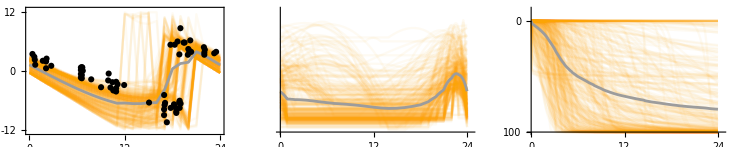

```mathematica
(*graphical illustration of the 327 pairs of gating and adaptation which were filtered out*)
adapcollect={};
gatingcollect={};

opa=0.05;
ft=18;

set={};
For[i=1,i<Dimensions[fffclass2][[1]]+1,i++,
set=Join[set,{{fffclass2[[i]][[5]],fffclass2[[i]][[6]],fffclass2[[i]][[3]],fffclass2[[i]][[4]],fffclass2[[i]][[2]],fffclass2[[i]][[1]]-24+fffclass2[[i]][[2]]}}];
];

For[i=1,i<Dimensions[set][[1]]+1,i++,

scale=set[[i]][[1]];
exponent=set[[i]][[2]];
perconst1=set[[i]][[3]];
perconst2=set[[i]][[4]];
interval=set[[i]][[5]];
rotate=set[[i]][[6]]*10;

adap[x_]:=-(x^exponent/(x^exponent+scale^exponent))+1;

pergating=NonlinearModelFit[{{24-interval,perconst1},{24,perconst1},{24-0.5*interval,perconst2}},q0+q1*x+q2*x^2+q3*x^3+q4*x^4,{q0,q1,q2,q3,q4},x];

interpol=Join[Table[perconst1,{x,0,24-interval,0.1}],Table[pergating[x],{x,24-interval+0.1,24,0.1}]];
interpol=RotateRight[interpol,rotate];
gatingcollect=Join[gatingcollect,{Table[interpol[[i+1]],{i,0,240}]}];
adapcollect=Join[adapcollect,{Table[adap[0.1*i],{i,0,240}]}];
];

classgraph=ListPlot[gatingcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[Black]];

adapgraph=ListPlot[adapcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.5,1},{"100","","0"}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[Black]];

meangating=Mean[gatingcollect];
meanadap=Mean[adapcollect];

meangatinggraph=ListPlot[meangating,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","6","","12"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[meancolor]];
meanadapgraph=ListPlot[meanadap,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{0,6,12,18,24}}],Transpose[{{0,0.5,1},{0,50,100}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[meancolor]];

ft=18;
opa=0.05;

cycle3mean=Mean[fffprc3cycleclass2];
prc3cyclegraph=ListPlot[fffprc3cycleclass2,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-12.5,12.5},Joined->True,FrameTicks->{{0,12,24},{-12,0,12}},Frame->{{True,None},{True,None}},PlotStyle->Directive[simulcolor,Opacity[opa]],FrameTicksStyle->Directive[Black],AxesStyle->Dashed];
mean3cyclegraph=ListPlot[cycle3mean,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-12.5,12.5},Joined->True,FrameTicks->{{0,12,24},{-12,-6,0,6,12}},Frame->{{True,None},{True,None}},PlotStyle->{meancolor,Thickness[0.005]}];

GraphicsGrid[{{Show[prc3cyclegraph,mean3cyclegraph,ex3cyclegraph],Show[classgraph,meangatinggraph],Show[adapgraph,meanadapgraph]}}]
```

```mathematica
(*99 pairs of gating and adaptation with which the model fails to simulate the human PRC to a 6.7 h light pulse between CT15 and CT18 were filtered out*)
ffffclass1={};
ffffprc3hrclass1={};
ffffprc67hrclass1={};
ffffprc12hrclass1={};
ffffldzt10class1={};
ffffprc3cycleclass1={};

ffffclass2={};
ffffprc3hrclass2={};
ffffprc67hrclass2={};
ffffprc12hrclass2={};
ffffldzt10class2={};
ffffprc3cycleclass2={};

For[i=1,i<Dimensions[fffclass1][[1]]+1,i++,
If[(fffprc67hrclass1[[i]][[6]]<0)&&(fffprc67hrclass1[[i]][[7]]>1),

ffffclass1=Join[ffffclass1,{fffclass1[[i]]}];
ffffprc3hrclass1=Join[ffffprc3hrclass1,{fffprc3hrclass1[[i]]}];
ffffprc67hrclass1=Join[ffffprc67hrclass1,{fffprc67hrclass1[[i]]}];
ffffprc12hrclass1=Join[ffffprc12hrclass1,{fffprc12hrclass1[[i]]}];
ffffldzt10class1=Join[ffffldzt10class1,{fffldzt10class1[[i]]}];
ffffprc3cycleclass1=Join[ffffprc3cycleclass1,{fffprc3cycleclass1[[i]]}];
,

ffffclass2=Join[ffffclass2,{fffclass1[[i]]}];
ffffprc3hrclass2=Join[ffffprc3hrclass2,{fffprc3hrclass1[[i]]}];
ffffprc67hrclass2=Join[ffffprc67hrclass2,{fffprc67hrclass1[[i]]}];
ffffprc12hrclass2=Join[ffffprc12hrclass2,{fffprc12hrclass1[[i]]}];
ffffldzt10class2=Join[ffffldzt10class2,{fffldzt10class1[[i]]}];
ffffprc3cycleclass2=Join[ffffprc3cycleclass2,{fffprc3cycleclass1[[i]]}];

 ];
];

(*{the number of parameter sets, which were filtered in, the number of parameter sets, which were filetered our}*)
Print[{Dimensions[ffffclass1],Dimensions[ffffclass2]}]
```

{{10,6},{99,6}}

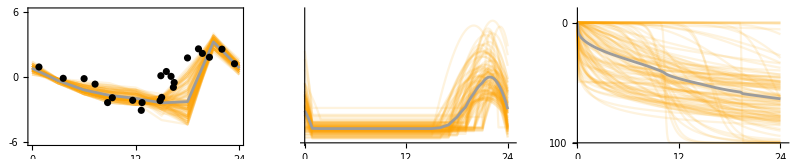

```mathematica
(*graphical illustration of the 99 pairs of gating and adaptation which were filtered out*)
adapcollect={};
gatingcollect={};

opa=0.13;
ft=18;

set={};
For[i=1,i<Dimensions[ffffclass2][[1]]+1,i++,
set=Join[set,{{ffffclass2[[i]][[5]],ffffclass2[[i]][[6]],ffffclass2[[i]][[3]],ffffclass2[[i]][[4]],ffffclass2[[i]][[2]],ffffclass2[[i]][[1]]-24+ffffclass2[[i]][[2]]}}];
];

For[i=1,i<Dimensions[set][[1]]+1,i++,

scale=set[[i]][[1]];
exponent=set[[i]][[2]];
perconst1=set[[i]][[3]];
perconst2=set[[i]][[4]];
interval=set[[i]][[5]];
rotate=set[[i]][[6]]*10;

adap[x_]:=-(x^exponent/(x^exponent+scale^exponent))+1;

pergating=NonlinearModelFit[{{24-interval,perconst1},{24,perconst1},{24-0.5*interval,perconst2}},q0+q1*x+q2*x^2+q3*x^3+q4*x^4,{q0,q1,q2,q3,q4},x];

interpol=Join[Table[perconst1,{x,0,24-interval,0.1}],Table[pergating[x],{x,24-interval+0.1,24,0.1}]];
interpol=RotateRight[interpol,rotate];
gatingcollect=Join[gatingcollect,{Table[interpol[[i+1]],{i,0,240}]}];
adapcollect=Join[adapcollect,{Table[adap[0.1*i],{i,0,240}]}];
];

classgraph=ListPlot[gatingcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[Black]];

adapgraph=ListPlot[adapcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.5,1},{"100","","0"}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[Black]];

meangating=Mean[gatingcollect];
meanadap=Mean[adapcollect];

meangatinggraph=ListPlot[meangating,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","6","","12"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[meancolor]];
meanadapgraph=ListPlot[meanadap,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{0,6,12,18,24}}],Transpose[{{0,0.5,1},{0,50,100}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[meancolor]];

ft=18;
meancp6=Mean[ffffprc67hrclass2];

cp6graph=ListPlot[ffffprc67hrclass2,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-6.1,6.1},Joined->True,FrameTicks->{{0,12,24},{-6,0,6}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Dashed];
meancp6graph=ListPlot[meancp6,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-9.1,9.1},Joined->True,FrameTicks->{{0,12,24},{-6,0,6}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->{meancolor,Thickness[0.005]}];

GraphicsGrid[{{Show[cp6graph,meancp6graph,ex67hrgraph],Show[classgraph,meangatinggraph],Show[adapgraph,meanadapgraph]}}]
```

```mathematica
(*10 pairs of gating and adaptation passed the filtering procesure*)
ffffclass1//MatrixForm
```

(19. | 5. | 0.0254792 | 0.0929286 | 6.46745 | 1.83047
15. | 11. | 0.0330412 | 0.114949 | 4.02134 | 0.987144
16. | 9. | 0.0118881 | 0.133646 | 9.31215 | 0.224981
20. | 4. | 0.0228344 | 0.104266 | 9.22827 | 3.23776
16. | 9. | 0.0143601 | 0.0909484 | 9.17072 | 1.43947
19. | 5. | 0.0219518 | 0.105984 | 7.67647 | 3.14733
16. | 10. | 0.0280037 | 0.133435 | 4.85414 | 0.342901
16. | 9. | 0.0156313 | 0.0932321 | 8.25925 | 1.78114
15. | 10. | 0.0140468 | 0.109908 | 6.91693 | 0.670481
16. | 9. | 0.0111993 | 0.0944462 | 16.9357 | 0.78709)

```mathematica
(*graphical illustration of the 10 pairs of gating and adaptation which were filtered in*)

adapcollect={};
gatingcollect={};

opa=0.13;
ft=18;

set={};
For[i=1,i<Dimensions[ffffclass1][[1]]+1,i++,
set=Join[set,{{ffffclass1[[i]][[5]],ffffclass1[[i]][[6]],ffffclass1[[i]][[3]],ffffclass1[[i]][[4]],ffffclass1[[i]][[2]],ffffclass1[[i]][[1]]-24+ffffclass1[[i]][[2]]}}];
];

For[i=1,i<Dimensions[set][[1]]+1,i++,

scale=set[[i]][[1]];
exponent=set[[i]][[2]];
perconst1=set[[i]][[3]];
perconst2=set[[i]][[4]];
interval=set[[i]][[5]];
rotate=set[[i]][[6]]*10;

adap[x_]:=-(x^exponent/(x^exponent+scale^exponent))+1;

pergating=NonlinearModelFit[{{24-interval,perconst1},{24,perconst1},{24-0.5*interval,perconst2}},q0+q1*x+q2*x^2+q3*x^3+q4*x^4,{q0,q1,q2,q3,q4},x];

interpol=Join[Table[perconst1,{x,0,24-interval,0.1}],Table[pergating[x],{x,24-interval+0.1,24,0.1}]];
interpol=RotateRight[interpol,rotate];
gatingcollect=Join[gatingcollect,{Table[interpol[[i+1]],{i,0,240}]}];
adapcollect=Join[adapcollect,{Table[adap[0.1*i],{i,0,240}]}];
];

classgraph=ListPlot[gatingcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[Black]];

adapgraph=ListPlot[adapcollect,DataRange->{0,24},Joined->True,PlotStyle->Directive[simulcolor,Opacity[opa]],AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","12","","24"}}],Transpose[{{0,0.5,1},{"100","","0"}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[Black]];

meangating=Mean[gatingcollect];
meanadap=Mean[adapcollect];

meangatinggraph=ListPlot[meangating,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{"0","","6","","12"}}],Transpose[{{0,0.1,0.2},{"","",""}}]},PlotRange->{{0,24.5},{0,0.215}},TicksStyle->Directive[meancolor]];
meanadapgraph=ListPlot[meanadap,DataRange->{0,24},Joined->True,PlotStyle->{meancolor,Thickness[0.005]},AxesStyle->Directive[Thick,FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesOrigin->{0,0},Ticks->{Transpose[{{0,6,12,18,24},{0,6,12,18,24}}],Transpose[{{0,0.5,1},{0,50,100}}]},PlotRange->{{0,24.5},{0,1.1}},TicksStyle->Directive[meancolor]];

ft=18;
meancp6=Mean[ffffprc67hrclass1];
meancp3=Mean[ffffprc3hrclass1];
cycle3mean=Mean[ffffprc3cycleclass1];

cp6graph=ListPlot[ffffprc67hrclass1,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-6.1,6.1},Joined->True,FrameTicks->{{0,12,24},{-6,0,6}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->Directive[simulcolor,Opacity[opa]]];
prc3cyclegraph=ListPlot[ffffprc3cycleclass1,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-12.5,12.5},Joined->True,FrameTicks->{{0,12,24},{-12,0,12}},Frame->{{True,None},{True,None}},PlotStyle->Directive[simulcolor,Opacity[opa]],FrameTicksStyle->Directive[Black],AxesStyle->Dashed];
cp3graph=ListPlot[ffffprc3hrclass1,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-6.1,6.1},Joined->True,FrameTicks->{{0,12,24},{-6,0,6}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[Black],PlotStyle->Directive[simulcolor,Opacity[opa]]];

meancp6graph=ListPlot[meancp6,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-9.1,9.1},Joined->True,FrameTicks->{{0,6,12,18,24},{-9,-6,-3,0,3,6,9}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[meancolor],PlotStyle->{meancolor,Thickness[0.005]}];
mean3cyclegraph=ListPlot[cycle3mean,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-12.5,12.5},Joined->True,FrameTicks->{{0,12,24},{-12,-6,0,6,12}},Frame->{{True,None},{True,None}},PlotStyle->{meancolor,Thickness[0.005]}];
meancp3graph=ListPlot[meancp3,DataRange->{0,24},Joined->True,FrameStyle->Directive[ft,Thick],
BaseStyle->{FontFamily->"Helvetica",FontSize->16},AxesOrigin->{0,0},PlotRange->{-6.1,6.1},Joined->True,FrameTicks->{{0,6,12,18,24},{-6,-3,0,3,6}},Frame->{{True,None},{True,None}},FrameTicksStyle->Directive[meancolor],PlotStyle->meancolor];
```

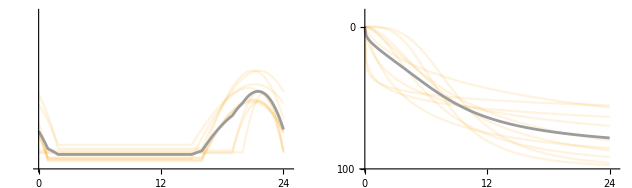

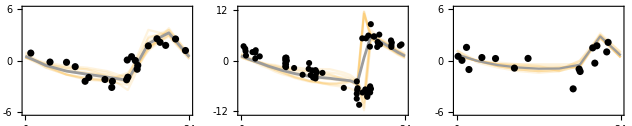

```mathematica
GraphicsGrid[{{Show[classgraph,meangatinggraph],Show[adapgraph,meanadapgraph]}}]
GraphicsGrid[{{Show[cp6graph,meancp6graph,ex67hrgraph],Show[prc3cyclegraph,mean3cyclegraph,ex3cyclegraph],Show[cp3graph,meancp3graph,ex3hrgraph]}}]
```